# Making graphs for puromycin

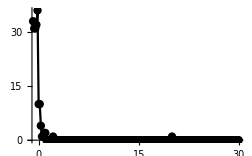
## Old graphing method : -Graphics- NO yellow vs white spots. Just showing # green spots colocalizing with red

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myFile = Import["/Volumes/MINI 1/_PURO/NT TA TL puro counts.xlsx"];
```

```mathematica
myTimes = myFile[[3,1;;All,3]];
myTransSpots = myFile[[3,1;;All,2]];
```

```mathematica
myData = {myTimes,myTransSpots}//Transpose;
```

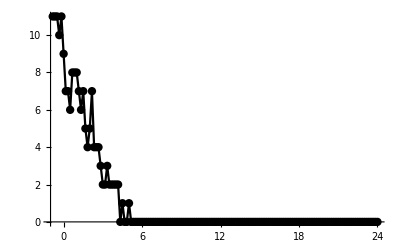

```mathematica
ListPlot[myData, PlotRange->All,Joined->True,AxesOrigin->{-1,0},PlotStyle->Black, Mesh->All]
```

```mathematica
Show[%334,PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

-Graphics-

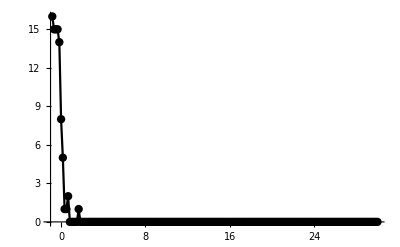

```mathematica
Show[%315,PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

```mathematica
Show[%317,PlotLabel->None]
```

-Graphics-

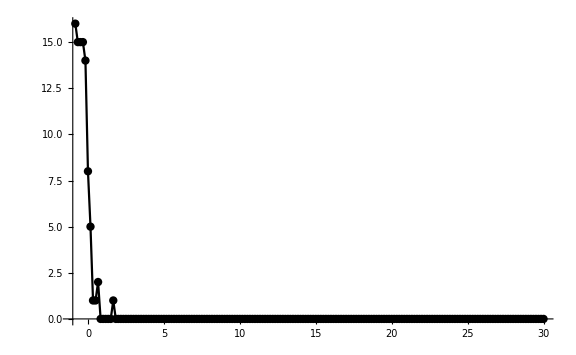

```mathematica
Show[%319,ImageSize->Large]
```

```mathematica
Show[%290,AxesLabel->{HoldForm[Time min],HoldForm[Number of translating RNA]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

```mathematica
Show[%316,ImageSize->Large]
```

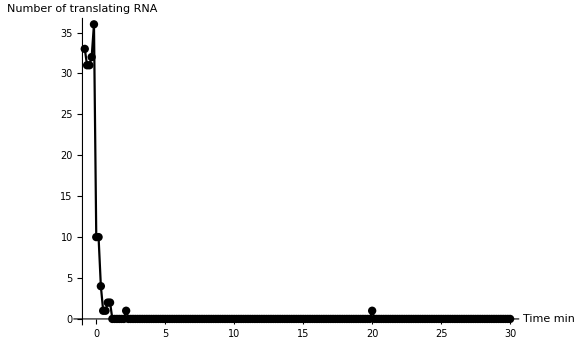

```mathematica
Show[%291,ImageSize->Large]
```

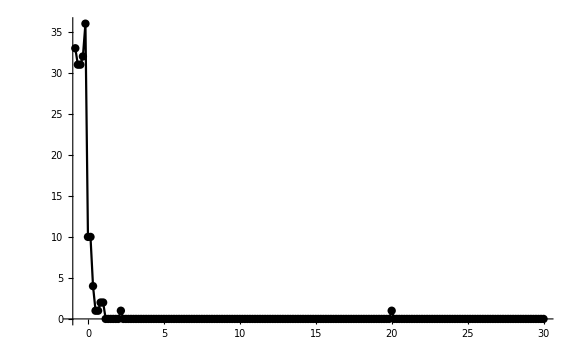

```mathematica
Show[%282,ImageSize->Large, FontSize-> 64]
```

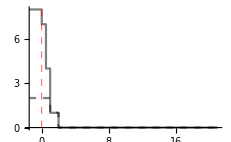
## New style : -Graphics- Survival plot,I reanalyzed these to look at green signal in either white or yellow spots, per cell

#### Parameters :

```mathematica
textfont = LabelStyle->{ FontFamily->"Arial Narrow",32,GrayLevel[.2]};
legend = PlotLegends-> {"Un-tethered, translating mRNA","Tethered, translating mRNA"};
```

#### Data :

Data :    { {yellow spot decay} , {white spot decay} }

```mathematica
excelbook1 = { {"2019 06 22-4","","TA09 Yel","TA09 Wht","TA20 Yel","TA20 Wht","","","","","yel","wt"},{-3.,1.,3.,3.,6.,1.,"","","","","",""},{-2.,2.,3.,3.,6.,1.,"","","","","",""},{-1.,3.,3.,3.,6.,1.,"","","","","",""},{0.,4.,3.,3.,6.,1.,"","","","","",""},{1.,5.,1.,3.,4.,1.,"","","","","",""},{2.,6.,1.,0.,1.,0.,"","","","","",""},{3.,7.,0.,0.,0.,0.,"","","","","",""},{4.,8.,0.,0.,0.,0.,"","","","","",""},{5.,9.,0.,0.,0.,0.,"","","","","",""},{6.,10.,0.,0.,0.,0.,"","","","","",""},{7.,11.,0.,0.,0.,0.,"","","","","",""},{8.,12.,0.,0.,0.,0.,"","","","","",""},{9.,13.,0.,0.,0.,0.,"","","","","",""},{10.,14.,0.,0.,0.,0.,"","","","","",""},{11.,15.,0.,0.,0.,0.,"","","","","",""},{12.,16.,0.,0.,0.,0.,"","","","","",""},{13.,17.,0.,0.,0.,0.,"","","","","",""},{14.,18.,0.,0.,0.,0.,"","","","","",""},{15.,19.,0.,0.,0.,0.,"","","","","",""},{16.,20.,0.,0.,0.,0.,"","","","","",""},{17.,21.,0.,0.,0.,0.,"","","","","",""},{18.,22.,0.,0.,0.,0.,"","","","","",""},{19.,23.,0.,0.,0.,0.,"","","","","",""},{20.,24.,0.,0.,0.,0.,"","","","","",""},{21.,25.,0.,0.,0.,0.,"","","","","",""},{22.,26.,0.,0.,0.,0.,"","","","","",""},{23.,27.,0.,0.,0.,0.,"","","","","",""},{24.,28.,0.,0.,0.,0.,"","","","","",""},{25.,29.,0.,0.,0.,0.,"","","","","",""},{26.,30.,0.,0.,0.,0.,"","","","","",""},{27.,31.,0.,0.,0.,0.,"","","","","",""},{28.,32.,0.,0.,0.,0.,"","","","","",""},{29.,33.,0.,0.,0.,0.,"","","","","",""},{30.,34.,0.,0.,0.,0.,"","","","","",""},{31.,35.,0.,0.,0.,0.,"","","","","",""},{32.,36.,0.,0.,0.,0.,"","","","","",""},{33.,37.,0.,0.,0.,0.,"","","","","",""},{34.,38.,0.,0.,0.,0.,"","","","","",""},{35.,39.,0.,0.,0.,0.,"","","","","",""},{36.,40.,0.,0.,0.,0.,"","","","","",""},{37.,41.,0.,0.,0.,0.,"","","","","",""},{38.,42.,0.,0.,0.,0.,"","","","","",""},{39.,43.,0.,0.,0.,0.,"","","","","",""},{40.,44.,0.,0.,0.,0.,"","","","","",""},{41.,45.,0.,0.,0.,0.,"","","","","",""},{42.,46.,0.,0.,0.,0.,"","","","","",""},{43.,47.,0.,0.,0.,0.,"","","","","",""},{44.,48.,0.,0.,0.,0.,"","","","","",""},{45.,49.,0.,0.,0.,0.,"","","","","",""},{46.,50.,0.,0.,0.,0.,"","","","","",""},{47.,51.,0.,0.,0.,0.,"","","","","",""},{48.,52.,0.,0.,0.,0.,"","","","","",""},{49.,53.,0.,0.,0.,0.,"","","","","",""},{50.,54.,0.,0.,0.,0.,"","","","","",""},{51.,55.,0.,0.,0.,0.,"","","","","",""},{52.,56.,0.,0.,0.,0.,"","","","","",""},{53.,57.,0.,0.,0.,0.,"","","","","",""},{54.,58.,0.,0.,0.,0.,"","","","","",""},{55.,59.,0.,0.,0.,0.,"","","","","",""},{56.,60.,0.,0.,0.,0.,"","","","","",""},{57.,61.,0.,0.,0.,0.,"","","","","",""},{58.,62.,0.,0.,0.,0.,"","","","","",""},{59.,63.,0.,0.,0.,0.,"","","","","",""},{60.,64.,0.,0.,0.,0.,"","","","","",""},{61.,65.,0.,0.,0.,0.,"","","","","",""}} ;
```

```mathematica
excelbook2 = { {"2019 06 22-4","","","NT02 yel","NT02 Wt","TA02 yel","TA02 wt"},{1.,-30.,-0.5,26.,0.,8.,6.},{2.,-20.,-0.3333333333333333,26.,0.,7.,6.},{3.,-10.,-0.16666666666666666,28.,0.,7.,6.},{4.,0.,0.,27.,0.,6.,6.},{5.,10.,0.16666666666666666,27.,0.,7.,3.},{6.,20.,0.3333333333333333,15.,0.,8.,3.},{7.,30.,0.5,4.,0.,3.,2.},{8.,40.,0.6666666666666666,3.,0.,2.,1.},{9.,50.,0.8333333333333334,5.,0.,1.,1.},{10.,60.,1.,2.,0.,0.,0.},{11.,70.,1.1666666666666667,1.,0.,0.,0.},{12.,80.,1.3333333333333333,1.,0.,0.,0.},{13.,90.,1.5,2.,0.,0.,0.},{14.,100.,1.6666666666666667,2.,0.,0.,0.},{15.,110.,1.8333333333333333,2.,0.,0.,0.},{16.,120.,2.,3.,0.,0.,0.},{17.,130.,2.1666666666666665,2.,0.,0.,0.},{18.,140.,2.3333333333333335,1.,0.,0.,0.},{19.,150.,2.5,1.,0.,0.,0.},{20.,160.,2.6666666666666665,1.,0.,0.,0.},{21.,170.,2.8333333333333335,1.,0.,0.,0.},{22.,180.,3.,1.,0.,0.,0.},{23.,190.,3.1666666666666665,1.,0.,0.,0.},{24.,200.,3.3333333333333335,1.,0.,0.,0.},{25.,210.,3.5,1.,0.,0.,0.},{26.,220.,3.6666666666666665,1.,0.,0.,0.},{27.,230.,3.8333333333333335,1.,0.,0.,0.},{28.,240.,4.,1.,0.,0.,0.},{29.,250.,4.166666666666667,1.,0.,0.,0.},{30.,260.,4.333333333333333,1.,0.,0.,0.},{31.,270.,4.5,1.,0.,0.,0.},{32.,280.,4.666666666666667,1.,0.,0.,0.},{33.,290.,4.833333333333333,1.,0.,0.,0.},{34.,300.,5.,1.,0.,0.,0.},{35.,310.,5.166666666666667,1.,0.,0.,0.},{36.,320.,5.333333333333333,1.,0.,0.,0.},{37.,330.,5.5,1.,0.,0.,0.},{38.,340.,5.666666666666667,1.,0.,0.,0.},{39.,350.,5.833333333333333,1.,0.,0.,0.},{40.,360.,6.,1.,0.,0.,0.},{41.,370.,6.166666666666667,1.,0.,0.,0.},{42.,380.,6.333333333333333,1.,0.,0.,0.},{43.,390.,6.5,1.,0.,0.,0.},{44.,400.,6.666666666666667,1.,0.,0.,0.},{45.,410.,6.833333333333333,0.,0.,0.,0.},{46.,420.,7.,0.,0.,0.,0.},{47.,430.,7.166666666666667,0.,0.,0.,0.},{48.,440.,7.333333333333333,0.,0.,0.,0.},{49.,450.,7.5,0.,0.,0.,0.},{50.,460.,7.666666666666667,0.,0.,0.,0.},{51.,470.,7.833333333333333,0.,0.,0.,0.},{52.,480.,8.,0.,0.,0.,0.},{53.,490.,8.166666666666666,0.,0.,0.,0.},{54.,500.,8.333333333333334,0.,0.,0.,0.},{55.,510.,8.5,0.,0.,0.,0.},{56.,520.,8.666666666666666,0.,0.,0.,0.},{57.,530.,8.833333333333334,0.,0.,0.,0.},{58.,540.,9.,0.,0.,0.,0.},{59.,550.,9.166666666666666,0.,0.,0.,0.},{60.,560.,9.333333333333334,0.,0.,0.,0.},{61.,570.,9.5,0.,0.,0.,0.},{62.,580.,9.666666666666666,0.,0.,0.,0.},{63.,590.,9.833333333333334,0.,0.,0.,0.},{64.,600.,10.,0.,0.,0.,0.},{65.,610.,10.166666666666666,0.,0.,0.,0.}} ;
```

```mathematica
excelbook3 ={{"2019 06 22-4","","","TL01 yel","TL01 Wt","","","","","","","yel","wt"},{1.,-30.,-0.5,3.,8.,"","","","","","","",""},{2.,-20.,-0.3333333333333333,3.,8.,"","","","","","","",""},{3.,-10.,-0.16666666666666666,3.,8.,"","","","","","","",""},{4.,0.,0.,3.,8.,"","","","","","","",""},{5.,10.,0.16666666666666666,3.,7.,"","","","","","","",""},{6.,20.,0.3333333333333333,3.,8.,"","","","","","","",""},{7.,30.,0.5,2.,7.,"","","","","","","",""},{8.,40.,0.6666666666666666,2.,7.,"","","","","","","",""},{9.,50.,0.8333333333333334,1.,6.,"","","","","","","",""},{10.,60.,1.,1.,6.,"","","","","","","",""},{11.,70.,1.1666666666666667,1.,5.,"","","","","","","",""},{12.,80.,1.3333333333333333,1.,6.,"","","","","","","",""},{13.,90.,1.5,1.,4.,"","","","","","","",""},{14.,100.,1.6666666666666667,1.,5.,"","","","","","","",""},{15.,110.,1.8333333333333333,1.,5.,"","","","","","","",""},{16.,120.,2.,1.,3.,"","","","","","","",""},{17.,130.,2.1666666666666665,1.,2.,"","","","","","","",""},{18.,140.,2.3333333333333335,2.,3.,"","","","","","","",""},{19.,150.,2.5,1.,4.,"","","","","","","",""},{20.,160.,2.6666666666666665,1.,4.,"","","","","","","",""},{21.,170.,2.8333333333333335,1.,3.,"","","","","","","",""},{22.,180.,3.,1.,3.,"","","","","","","",""},{23.,190.,3.1666666666666665,1.,3.,"","","","","","","",""},{24.,200.,3.3333333333333335,1.,3.,"","","","","","","",""},{25.,210.,3.5,1.,3.,"","","","","","","",""},{26.,220.,3.6666666666666665,2.,2.,"","","","","","","",""},{27.,230.,3.8333333333333335,1.,2.,"","","","","","","",""},{28.,240.,4.,1.,3.,"","","","","","","",""},{29.,250.,4.166666666666667,1.,2.,"","","","","","","",""},{30.,260.,4.333333333333333,1.,1.,"","","","","","","",""},{31.,270.,4.5,0.,1.,"","","","","","","",""},{32.,280.,4.666666666666667,0.,1.,"","","","","","","",""},{33.,290.,4.833333333333333,0.,1.,"","","","","","","",""},{34.,300.,5.,1.,1.,"","","","","","","",""},{35.,310.,5.166666666666667,0.,0.,"","","","","","","",""},{36.,320.,5.333333333333333,0.,0.,"","","","","","","",""},{37.,330.,5.5,0.,0.,"","","","","","","",""},{38.,340.,5.666666666666667,0.,0.,"","","","","","","",""},{39.,350.,5.833333333333333,0.,0.,"","","","","","","",""},{40.,360.,6.,0.,0.,"","","","","","","",""},{41.,370.,6.166666666666667,0.,0.,"","","","","","","",""},{42.,380.,6.333333333333333,0.,0.,"","","","","","","",""},{43.,390.,6.5,0.,0.,"","","","","","","",""},{44.,400.,6.666666666666667,0.,0.,"","","","","","","",""},{45.,410.,6.833333333333333,0.,0.,"","","","","","","",""},{46.,420.,7.,0.,0.,"","","","","","","",""},{47.,430.,7.166666666666667,0.,0.,"","","","","","","",""},{48.,440.,7.333333333333333,0.,0.,"","","","","","","",""},{49.,450.,7.5,0.,0.,"","","","","","","",""},{50.,460.,7.666666666666667,0.,0.,"","","","","","","",""},{51.,470.,7.833333333333333,0.,0.,"","","","","","","",""},{52.,480.,8.,0.,0.,"","","","","","","",""},{53.,490.,8.166666666666666,0.,0.,"","","","","","","",""},{54.,500.,8.333333333333334,0.,0.,"","","","","","","",""},{55.,510.,8.5,0.,0.,"","","","","","","",""},{56.,520.,8.666666666666666,0.,0.,"","","","","","","",""},{57.,530.,8.833333333333334,0.,0.,"","","","","","","",""},{58.,540.,9.,0.,0.,"","","","","","","",""},{59.,550.,9.166666666666666,0.,0.,"","","","","","","",""},{60.,560.,9.333333333333334,0.,0.,"","","","","","","",""},{61.,570.,9.5,0.,0.,"","","","","","","",""},{62.,580.,9.666666666666666,0.,0.,"","","","","","","",""},{63.,590.,9.833333333333334,0.,0.,"","","","","","","",""},{64.,600.,10.,0.,0.,"","","","","","","",""},{65.,610.,10.166666666666666,0.,0.,"","","","","","","",""}};
```

```mathematica
excelbook4 =  {{"2019 06 22-4","frame","TL 01 Yel","TL 01 Wt ","TL 13 Yel","TL 13 Wt","","","","","yel","wt"},{-1.5,1.,3.,9.,2.,8.,"","","","","",""},{-1.,2.,4.,9.,2.,8.,"","","","","",""},{-0.5,3.,3.,8.,2.,8.,"","","","","",""},{0.,4.,3.,9.,2.,7.,"","","","","",""},{0.5,5.,1.,4.,2.,4.,"","","","","",""},{1.,6.,0.,0.,1.,1.,"","","","","",""},{1.5,7.,0.,0.,1.,1.,"","","","","",""},{2.,8.,0.,0.,0.,0.,"","","","","",""},{2.5,9.,0.,0.,0.,0.,"","","","","",""},{3.,10.,0.,0.,0.,0.,"","","","","",""},{3.5,11.,0.,0.,0.,0.,"","","","","",""},{4.,12.,0.,0.,0.,0.,"","","","","",""},{4.5,13.,0.,0.,0.,0.,"","","","","",""},{5.,14.,0.,0.,0.,0.,"","","","","",""},{5.5,15.,0.,0.,0.,0.,"","","","","",""},{6.,16.,0.,0.,0.,0.,"","","","","",""},{6.5,17.,0.,0.,0.,0.,"","","","","",""},{7.,18.,0.,0.,0.,0.,"","","","","",""},{7.5,19.,0.,0.,0.,0.,"","","","","",""},{8.,20.,0.,0.,0.,0.,"","","","","",""},{8.5,21.,0.,0.,0.,0.,"","","","","",""},{9.,22.,0.,0.,0.,0.,"","","","","",""},{9.5,23.,0.,0.,0.,0.,"","","","","",""},{10.,24.,0.,0.,0.,0.,"","","","","",""},{10.5,25.,0.,0.,0.,0.,"","","","","",""},{11.,26.,0.,0.,0.,0.,"","","","","",""},{11.5,27.,0.,0.,0.,0.,"","","","","",""},{12.,28.,0.,0.,0.,0.,"","","","","",""},{12.5,29.,0.,0.,0.,0.,"","","","","",""},{13.,30.,0.,0.,0.,0.,"","","","","",""},{13.5,31.,0.,0.,0.,0.,"","","","","",""},{14.,32.,0.,0.,0.,0.,"","","","","",""},{14.5,33.,0.,0.,0.,0.,"","","","","",""},{15.,34.,0.,0.,0.,0.,"","","","","",""},{15.5,35.,0.,0.,0.,0.,"","","","","",""},{16.,36.,0.,0.,0.,0.,"","","","","",""},{16.5,37.,0.,0.,0.,0.,"","","","","",""},{17.,38.,0.,0.,0.,0.,"","","","","",""},{17.5,39.,0.,0.,0.,0.,"","","","","",""},{18.,40.,0.,0.,0.,0.,"","","","","",""},{18.5,41.,0.,0.,0.,0.,"","","","","",""},{19.,42.,0.,0.,0.,0.,"","","","","",""},{19.5,43.,0.,0.,0.,0.,"","","","","",""},{20.,44.,0.,0.,0.,0.,"","","","","",""},{20.5,45.,0.,0.,0.,0.,"","","","","",""}};
```

#### Code :

```mathematica
times1 = excelbook1[[2;;All,1]]
times2= excelbook2[[2;;All,3]]
times3= times2;
times4= excelbook4[[2;;All,1]]
```

{-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.}

{-0.5,-0.333333,-0.166667,0.,0.166667,0.333333,0.5,0.666667,0.833333,1.,1.16667,1.33333,1.5,1.66667,1.83333,2.,2.16667,2.33333,2.5,2.66667,2.83333,3.,3.16667,3.33333,3.5,3.66667,3.83333,4.,4.16667,4.33333,4.5,4.66667,4.83333,5.,5.16667,5.33333,5.5,5.66667,5.83333,6.,6.16667,6.33333,6.5,6.66667,6.83333,7.,7.16667,7.33333,7.5,7.66667,7.83333,8.,8.16667,8.33333,8.5,8.66667,8.83333,9.,9.16667,9.33333,9.5,9.66667,9.83333,10.,10.1667}

{-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5}

```mathematica
excelbook1[[1,3;;6]]
```

{TA09 Yel,TA09 Wht,TA20 Yel,TA20 Wht}

```mathematica
cellTA09 = excelbook1[[2;;All,3;;4]];
cellTA20 =  excelbook1[[2;;All,5;;6]];
```

```mathematica
Table[ Transpose@ { times1, cellTA09[[All,i]] } , {i,1,2}]
```

{{{-3.,3.},{-2.,3.},{-1.,3.},{0.,3.},{1.,1.},{2.,1.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.},{18.,0.},{19.,0.},{20.,0.},{21.,0.},{22.,0.},{23.,0.},{24.,0.},{25.,0.},{26.,0.},{27.,0.},{28.,0.},{29.,0.},{30.,0.},{31.,0.},{32.,0.},{33.,0.},{34.,0.},{35.,0.},{36.,0.},{37.,0.},{38.,0.},{39.,0.},{40.,0.},{41.,0.},{42.,0.},{43.,0.},{44.,0.},{45.,0.},{46.,0.},{47.,0.},{48.,0.},{49.,0.},{50.,0.},{51.,0.},{52.,0.},{53.,0.},{54.,0.},{55.,0.},{56.,0.},{57.,0.},{58.,0.},{59.,0.},{60.,0.},{61.,0.}},{{-3.,3.},{-2.,3.},{-1.,3.},{0.,3.},{1.,3.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.},{18.,0.},{19.,0.},{20.,0.},{21.,0.},{22.,0.},{23.,0.},{24.,0.},{25.,0.},{26.,0.},{27.,0.},{28.,0.},{29.,0.},{30.,0.},{31.,0.},{32.,0.},{33.,0.},{34.,0.},{35.,0.},{36.,0.},{37.,0.},{38.,0.},{39.,0.},{40.,0.},{41.,0.},{42.,0.},{43.,0.},{44.,0.},{45.,0.},{46.,0.},{47.,0.},{48.,0.},{49.,0.},{50.,0.},{51.,0.},{52.,0.},{53.,0.},{54.,0.},{55.,0.},{56.,0.},{57.,0.},{58.,0.},{59.,0.},{60.,0.},{61.,0.}}}

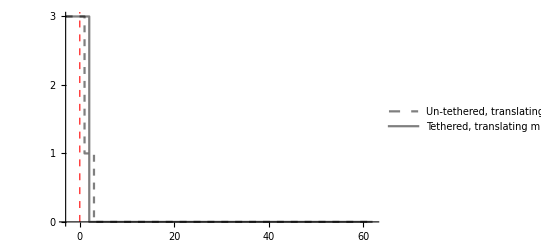

```mathematica
temptime = times1;
tempcell = cellTA09 ;
Show[ 
ListStepPlot[Table[ Transpose@ { temptime, tempcell[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont , AxesOrigin->{temptime[[1]],0}  ,   Ticks-> { Range[0,60,10] , Range[0,3,1] }] , 
ListLinePlot[{{0,0},{0,1 + Max@Flatten@tempcell} } , PlotStyle->{Red,Dashed , Thickness[.002]}]
]
```

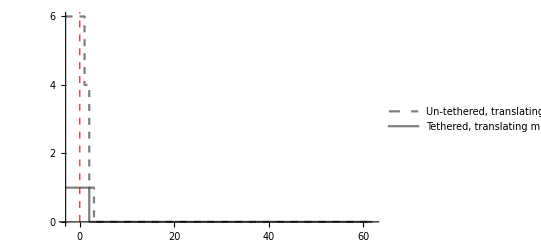

```mathematica
temptime = times1;
tempcell = cellTA20 ;
Show[ 
ListStepPlot[Table[ Transpose@ { temptime, tempcell[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont , AxesOrigin->{temptime[[1]],0} ,  Ticks-> { Range[0,60,10] , Range[0,6,2] }] , 
ListLinePlot[{{0,0},{0,1 + Max@Flatten@tempcell} } , PlotStyle->{Red,Dashed , Thickness[.002]}]
]
```

```mathematica
cellNT02 = excelbook2[[2;;All,4;;5]] ;
cellTA02 = excelbook2[[2;;All,6;;7]] ;
```

```mathematica
Length@cellNT02
times2
```

65

{-0.5,-0.333333,-0.166667,0.,0.166667,0.333333,0.5,0.666667,0.833333,1.,1.16667,1.33333,1.5,1.66667,1.83333,2.,2.16667,2.33333,2.5,2.66667,2.83333,3.,3.16667,3.33333,3.5,3.66667,3.83333,4.,4.16667,4.33333,4.5,4.66667,4.83333,5.,5.16667,5.33333,5.5,5.66667,5.83333,6.,6.16667,6.33333,6.5,6.66667,6.83333,7.,7.16667,7.33333,7.5,7.66667,7.83333,8.,8.16667,8.33333,8.5,8.66667,8.83333,9.,9.16667,9.33333,9.5,9.66667,9.83333,10.,10.1667}

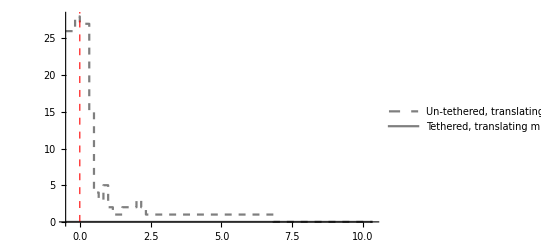

```mathematica
temptime = times2;
tempcell = cellNT02 ;
Show[ 
ListStepPlot[Table[ Transpose@ { temptime, tempcell[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont , AxesOrigin->{temptime[[1]],0}] , 
ListLinePlot[{{0,0},{0,1 + Max@Flatten@tempcell} } , PlotStyle->{Red,Dashed , Thickness[.002]}]
]
```

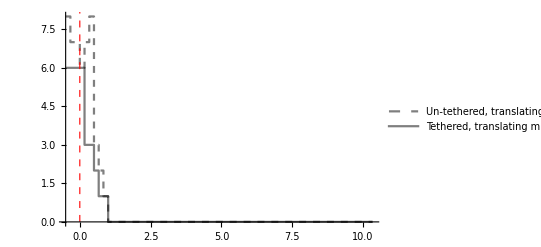

```mathematica
temptime = times2;
tempcell = cellTA02 ;
Show[ 
ListStepPlot[Table[ Transpose@ { temptime, tempcell[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont , AxesOrigin->{temptime[[1]],0}] , 
ListLinePlot[{{0,0},{0,1 + Max@Flatten@tempcell} } , PlotStyle->{Red,Dashed , Thickness[.002]}]
]
```

```mathematica
(*TL01 to TL0b bc TL01 was taken.... *)
excelbook3[[1 , 4;;5]]
cellTL01b = excelbook3[[2;;All,4;;5]]
Length/@{times3, cellTL01b}
```

{TL01 yel,TL01 Wt}

{{3.,8.},{3.,8.},{3.,8.},{3.,8.},{3.,7.},{3.,8.},{2.,7.},{2.,7.},{1.,6.},{1.,6.},{1.,5.},{1.,6.},{1.,4.},{1.,5.},{1.,5.},{1.,3.},{1.,2.},{2.,3.},{1.,4.},{1.,4.},{1.,3.},{1.,3.},{1.,3.},{1.,3.},{1.,3.},{2.,2.},{1.,2.},{1.,3.},{1.,2.},{1.,1.},{0.,1.},{0.,1.},{0.,1.},{1.,1.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

{65,65}

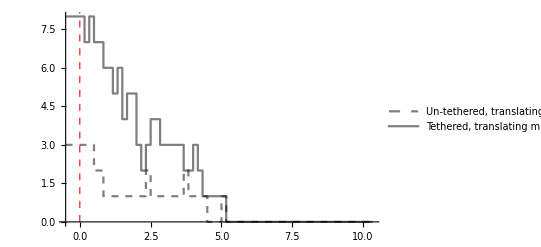

```mathematica
temptime = times3;
tempcell = cellTL01b ;
Show[ 
ListStepPlot[Table[ Transpose@ { temptime, tempcell[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont , AxesOrigin->{temptime[[1]],0}] , 
ListLinePlot[{{0,0},{0,1 + Max@Flatten@tempcell} } , PlotStyle->{Red,Dashed , Thickness[.002]}]
]
```

```mathematica
(*TL01 ... TL0b is shitty TL cell  .... *)
excelbook4[[1 , 3;;4]]
cellTL01= excelbook4[[2;;All,3;;4]];
Length/@{times4, cellTL01}
```

{TL 01 Yel,TL 01 Wt }

{45,45}

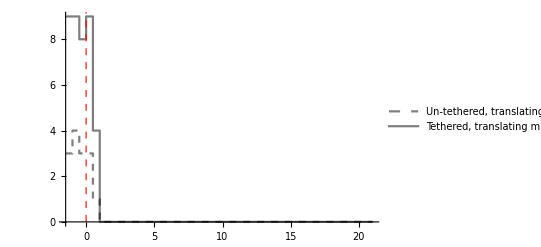

```mathematica
temptime = times4;
tempcell = cellTL01 ;
Show[ 
ListStepPlot[Table[ Transpose@ { temptime, tempcell[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont , AxesOrigin->{temptime[[1]],0}] , 
ListLinePlot[{{0,0},{0,1 + Max@Flatten@tempcell} } , PlotStyle->{Red,Dashed , Thickness[.002]}]
]
```

```mathematica
excelbook4[[1 , 5;;6]]
cellTL13= excelbook4[[2;;All, 5;;6]]
Length/@{times4, cellTL13}
```

{TL 13 Yel,TL 13 Wt}

{{2.,8.},{2.,8.},{2.,8.},{2.,7.},{2.,4.},{1.,1.},{1.,1.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

{45,45}

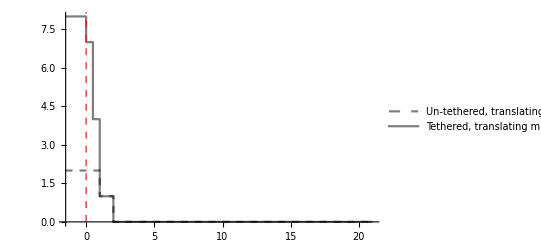

```mathematica
temptime = times4;
tempcell = cellTL13 ;
Show[ 
ListStepPlot[Table[ Transpose@ { temptime, tempcell[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont , AxesOrigin->{temptime[[1]],0}] , 
ListLinePlot[{{0,0},{0,1 + Max@Flatten@tempcell} } , PlotStyle->{Red,Dashed , Thickness[.002]}]
]
```